```mathematica
Integrate[α*Exp[-(w*x1+(1-w)*x2-θ)^2/τ^2]*(w*PDF[NormalDistribution[mu1,sig],x1]+(1-w)*PDF[NormalDistribution[mu2,sig],x2]),{x1,-Infinity,Infinity},{x2,-Infinity,Infinity}]
```

ConditionalExpression[-(√π α (-√(1/sig^2) √((-1+w)^2/τ^2)+√(1/sig^2) w √((-1+w)^2/τ^2)-w √(w^2/(2 sig^2 (-1+w)^2+τ^2)) √((2 sig^2 (-1+w)^2+τ^2)/(sig^2 τ^2))))/(√(1/sig^2) sig √((-1+w)^2/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2)) √((2 sig^2 (-1+w)^2+τ^2)/(sig^2 τ^2))),Re[w^2/(2 sig^2 (-1+w)^2+τ^2)]≥0&&Re[sig^2]≥0]

```mathematica
α*Exp[-(w*x1+(1-w)*x2-θ)^2/τ^2]*(w*PDF[NormalDistribution[mu1,sig1],x1]+(1-w)*PDF[NormalDistribution[mu2,sig2],x2])
```

ⅇ^(-(w x1+(1-w) x2-θ)^2/τ^2) ((ⅇ^(-(-mu2+x2)^2/(2 sig2^2)) (1-w))/(√(2 π) sig2)+(ⅇ^(-(-mu1+x1)^2/(2 sig1^2)) w)/(√(2 π) sig1)) α

```mathematica
FullSimplify[%]
```

$Aborted

```mathematica
Assuming[w≥0&&w≤1&&sig^2>0,
Integrate[α*Exp[-(w*x1+(1-w)*x2-θ)^2/τ^2]*(w*PDF[NormalDistribution[mu1,sig],x1]+(1-w)*PDF[NormalDistribution[mu2,sig],x2]),{x1,-Infinity,Infinity},{x2,-Infinity,Infinity}]]
```

$Aborted

```mathematica
FullSimplify[-(√π α (-√(1/sig^2) √((-1+w)^2/τ^2)+√(1/sig^2) w √((-1+w)^2/τ^2)-w √(w^2/(2 sig^2 (-1+w)^2+τ^2)) √((2 sig^2 (-1+w)^2+τ^2)/(sig^2 τ^2))))/(√(1/sig^2) sig √((-1+w)^2/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2)) √((2 sig^2 (-1+w)^2+τ^2)/(sig^2 τ^2)))]
```

(√π sig α τ^2 ((√(1/sig^2) w^3)/(√((-1+w)^2/τ^2) τ^2)+√(1/sig^2+(2 (-1+w)^2)/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2))-w √(1/sig^2+(2 (-1+w)^2)/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2))))/w^2

```mathematica
Manipulate[
Plot[1/w^2 √π sig α τ^2 ((√(1/sig^2) w^3)/(√((-1+w)^2/τ^2) τ^2)+√(1/sig^2+(2 (-1+w)^2)/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2))-w √(1/sig^2+(2 (-1+w)^2)/τ^2) √(w^2/(2 sig^2 (-1+w)^2+τ^2))),{w,0,1}],{sig,0.001,5},{τ,0.001,5},{α,5,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumr: The integrand ⅇ^(-1/4 (10+w x1+(1+Times[«2»]) x2)^2) ((ⅇ^(-1/2 (-5+x2)^2) (1-w))/(√(2 π))+(ⅇ^(-1/2 (5+x1)^2) w)/(√(2 π))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1000,1000},{-1000,1000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

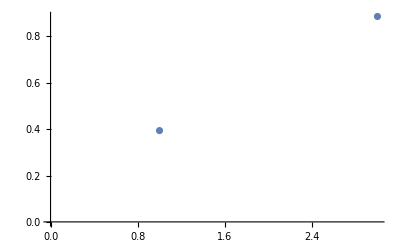

```mathematica
With[{θ=-10,mu1=-5,mu2=5},
ListPlot[
Table[
NIntegrate[1*Exp[-(w*x1+(1-w)*x2-θ)^2/2^2]*(w*(ⅇ^(-1/2 (-mu1+x1)^2))/(√(2 π))+(1-w)*(ⅇ^(-1/2 (-mu2+x2)^2))/(√(2 π))),{x1,-1000,1000},{x2,-1000,1000}],{w,0.1,0.2,0.05}]
]
]
```

```mathematica
PDF[NormalDistribution[mu1,1],x1]
PDF[NormalDistribution[mu2,1],x2]
```

(ⅇ^(-1/2 (-mu1+x1)^2))/(√(2 π))

(ⅇ^(-1/2 (-mu2+x2)^2))/(√(2 π))